In this notebook, we calculate the critical sensitivity, chi_u^*, as a function of the diffusivity of H-type individuals Dv and the wavenumber m, as studied in Section 3.2.2 of the main text and Section B.3 of the appendix. These calculations are used to produce Figure 2 and Figure 9, which are generated using MATLAB. The results from this notebook are cross-verified with the MATLAB scripts “chi_u_Dv_di.m” and “combine_chi_u.m”, ensuring consistency between the outputs.

The first part analytically calculates the critical chi_u^* under the equation detA=0, which corresponds to one of the stability conditions, detA>0.

```mathematica
ClearAll[c11,c12,c13,c22,c23,c32,c33,m,L,Du,Dv,Dn,p0,q0,chiu,chiv]

A={{c11-(m Pi/L)^2 (Du p0+Dv (1-p0)),c12-(m Pi/L)^2 (Du-Dv) q0,c13+(m Pi/L)^2 (chiu p0 q0+chiv q0 (1-p0))},{-q0^(-1) (m Pi/L)^2 (1-p0) p0 (Du-Dv),c22-(m Pi/L)^2 (Du (1-p0)+Dv p0),c23+(m Pi/L)^2 p0 (1-p0) (chiu-chiv)},{0,c32,-(m Pi/L)^2 Dn+c33}};

detA=Det[A];
eqn=detA==0;
solution=Solve[eqn,chiu];
solution
```

{{chiu→((c32 chiv (Du-Dv) m^4 (1-p0)^2 p0 π^4)/L^4+c23 c32 (c11-(m^2 (Dv (1-p0)+Du p0) π^2)/L^2)-(c32 chiv m^2 (1-p0) p0 π^2 (c11-(m^2 (Dv (1-p0)+Du p0) π^2)/L^2))/L^2+(c13 c32 (Du-Dv) m^2 (1-p0) p0 π^2)/(L^2 q0)-(c33-(Dn m^2 π^2)/L^2) ((c11-(m^2 (Dv (1-p0)+Du p0) π^2)/L^2) (c22-(m^2 (Du (1-p0)+Dv p0) π^2)/L^2)+((Du-Dv) m^2 (1-p0) p0 π^2 (c12-((Du-Dv) m^2 π^2 q0)/L^2))/(L^2 q0)))/(-(c32 (Du-Dv) m^4 (1-p0) p0^2 π^4)/L^4-(c32 m^2 (1-p0) p0 π^2 (c11-(m^2 (Dv (1-p0)+Du p0) π^2)/L^2))/L^2)}}

In the second part, we use the results from the first part and combine them with actual parameters to plot the minimum chi_u^*  as a function of diffusivity Dv under detA=0. This result is consistent with Figure 2 and the MATLAB script “chi_u_Dv_di.m”. The algorithm involves looping over different values of Dv , and for each Dv , iterating through different m values to identify the minimum chi_u^* across the range of m.

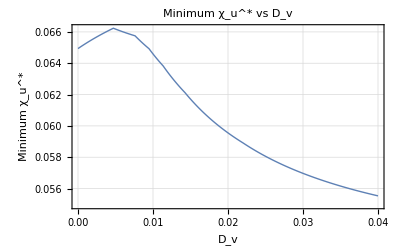

```mathematica
p0=0.5;
n0=0.5;
q0=4000;
L=10;
Du=0.01;
Dn=0.01;
chiv=0.02;
r=1;
a=0.5;
eL=0.2;
eH=0.5;
R0=0.35;
S0=0.3;
T0=0.5;
P0=0.2;
R1=0.6;
S1=0.35;
T1=0.6;
P1=0.3;
epsilon=10;
kappa=0.0001;

fL=(1-n0) (R0 p0+S0 (1-p0))+n0 (R1 p0+S1 (1-p0));
fH=(1-n0) (T0 p0+P0 (1-p0))+n0 (T1 p0+P1 (1-p0));

fLp=(1-n0) (R0-S0)+n0 (R1-S1);
fHp=(1-n0) (T0-P0)+n0 (T1-P1);
fLn=p0 (R1-R0)+(1-p0) (S1-S0);
fHn=p0 (T1-T0)+(1-p0) (P1-P0);
kp=fLp-fHp;
kn=fLn-fHn;

c11=((1-p0) fH+p0 fL-2 kappa q0)/epsilon;
c12=(q0 (fHp+p0 kp))/epsilon;
c13=(q0 (fHn+p0 kn))/epsilon;
c22=(p0 (1-p0) kp)/epsilon;
c23=(p0 (1-p0) kn)/epsilon;
c32=r-a (eL n0+eH (1-n0));
c33=-(r-a (eL n0+eH (1-n0)));

ChiU[m_,Dv_]:=Module[{chiuNum,chiuDen,chiuStar},
chiuNum=((c32 chiv (Du-Dv) m^4 (1-p0)^2 p0 π^4)/L^4+c23 c32 (c11-(m^2 (Dv (1-p0)+Du p0) π^2)/L^2)-(c32 chiv m^2 (1-p0) p0 π^2 (c11-(m^2 (Dv (1-p0)+Du p0) π^2)/L^2))/L^2+(c13 c32 (Du-Dv) m^2 (1-p0) p0 π^2)/(L^2 q0)-(c33-(Dn m^2 π^2)/L^2) ((c11-(m^2 (Dv (1-p0)+Du p0) π^2)/L^2) (c22-(m^2 (Du (1-p0)+Dv p0) π^2)/L^2)+((Du-Dv) m^2 (1-p0) p0 π^2 (c12-((Du-Dv) m^2 π^2 q0)/L^2))/(L^2 q0)));
chiuDen=(-(c32 (Du-Dv) m^4 (1-p0) p0^2 π^4)/L^4-(c32 m^2 (1-p0) p0 π^2 (c11-(m^2 (Dv (1-p0)+Du p0) π^2)/L^2))/L^2);
chiuStar=If[chiuDen==0||Im[chiuNum/chiuDen]!=0,∞,chiuNum/chiuDen];
chiuStar]

DvValues=Range[0,0.04,0.00001];
mValues=Range[0,100,1];

minChiUStar=Table[Min[Table[ChiU[m,Dv],{m,mValues}]],{Dv,DvValues}];

ListLinePlot[Transpose[{DvValues,minChiUStar}],PlotStyle->Thick,AxesLabel->{"D_v","Minimum χ_u^*"},PlotLabel->"Minimum χ_u^* vs D_v",GridLines->Automatic,Frame->True,PlotRange->All]
```

In the third part, we aim to analytically derive the expression for the critical chi_u^* under the equation -1/2 (trA2-trA^2) trA+detA=0, which corresponds to the other stability condition, -1/2 (trA2-trA^2) trA+detA>0.

```mathematica
ClearAll[c11,c12,c13,c22,c23,c32,c33,m,L,Du,Dv,Dn,p0,q0,chiu,chiv]

A={{c11-(m Pi/L)^2 (Du p0+Dv (1-p0)),c12-(m Pi/L)^2 (Du-Dv) q0,c13+(m Pi/L)^2 (chiu p0 q0+chiv q0 (1-p0))},{-q0^(-1) (m Pi/L)^2 (1-p0) p0 (Du-Dv),c22-(m Pi/L)^2 (Du (1-p0)+Dv p0),c23+(m Pi/L)^2 p0 (1-p0) (chiu-chiv)},{0,c32,-(m Pi/L)^2 Dn+c33}};

detA=Det[A];
trA=Tr[A];

A2=A.A;
trA2=Tr[A2];

eqn=-1/2 (trA2-trA^2) trA+detA==0;
solution=Solve[eqn,chiu];
FullSimplify[solution]
```

{{chiu→(c11 c12 (Du-Dv) L^4 m^2 (-1+p0) p0 π^2-c13 c32 (Du-Dv) L^4 m^2 (-1+p0) p0 π^2+c12 (Du-Dv) L^2 m^2 (-1+p0) p0 π^2 ((c22+2 c33) L^2-(2 Dn+Du+Dv) m^2 π^2)+c11^2 L^4 (-((c22+c33) L^2)+m^2 (Dn+Du-Du p0+Dv p0) π^2) q0-c11 L^2 ((c22^2-2 c23 c32+4 c22 c33+c33^2) L^4-2 L^2 m^2 (c22 (2 Dn+Du+Dv)+c32 chiv (-1+p0) p0+c33 (Dn+2 Du+Dv-Du p0+Dv p0)) π^2+m^4 (Dn^2+4 Dn Du+Du^2+2 Dn Dv+2 Du Dv-(Du-Dv) (2 Dn+Du+Dv) p0) π^4) q0+(-((c22+c33) (-c23 c32+c22 c33) L^6)+L^4 m^2 (c33^2 (Du+Dv)+c22 c32 chiv (-1+p0) p0+c32 c33 chiv (-1+p0) p0+c22^2 (Dn+Dv+Du p0-Dv p0)-c23 c32 (Dn+Du+2 Dv+Du p0-Dv p0)+2 c22 c33 (Dn+Du+2 Dv+Du p0-Dv p0)) π^2-L^2 m^4 (c33 (Du^2+4 Du Dv+Dv^2+2 Dn (Du+Dv))+c32 chiv (Dn+2 Du+Dv) (-1+p0) p0+c22 (Dn^2+2 Dn Du+4 Dn Dv+2 Du Dv+Dv^2+(Du-Dv) (2 Dn+Du+Dv) p0)) π^4+(Dn^2 (Du+Dv)+Du Dv (Du+Dv)+Dn (Du^2+4 Du Dv+Dv^2)) m^6 π^6) q0)/(c32 L^2 m^2 (-1+p0) p0 π^2 ((2 c11+c22+c33) L^2-(Dn+Du+2 Dv) m^2 π^2) q0)}}

In the fourth part, we use the results derived in the third part and combine them with actual parameters to plot the minimum chi_u^* as a function of diffusivity Dv under the equation -1/2 (trA2-trA^2) trA+detA=0. This result aligns with part of Figure 9 and the MATLAB script “combine_chi_u.m”. The algorithm follows the same approach as in the second part, with the only difference being the use of the new expression for critical chi_u^*

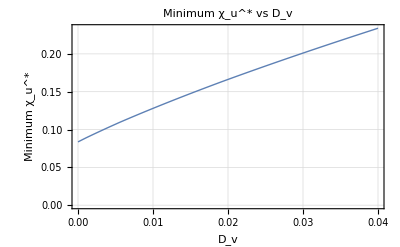

```mathematica
p0=0.5;
n0=0.5;
q0=4000;
L=10;
Du=0.01;
Dn=0.01;
chiv=0.02;
r=1;
a=0.5;
eL=0.2;
eH=0.5;
R0=0.35;
S0=0.3;
T0=0.5;
P0=0.2;
R1=0.6;
S1=0.35;
T1=0.6;
P1=0.3;
epsilon=10;
kappa=0.0001;

fL=(1-n0) (R0 p0+S0 (1-p0))+n0 (R1 p0+S1 (1-p0));
fH=(1-n0) (T0 p0+P0 (1-p0))+n0 (T1 p0+P1 (1-p0));

fLp=(1-n0) (R0-S0)+n0 (R1-S1);
fHp=(1-n0) (T0-P0)+n0 (T1-P1);
fLn=p0 (R1-R0)+(1-p0) (S1-S0);
fHn=p0 (T1-T0)+(1-p0) (P1-P0);
kp=fLp-fHp;
kn=fLn-fHn;

c11=((1-p0) fH+p0 fL-2 kappa q0)/epsilon;
c12=(q0 (fHp+p0 kp))/epsilon;
c13=(q0 (fHn+p0 kn))/epsilon;
c22=(p0 (1-p0) kp)/epsilon;
c23=(p0 (1-p0) kn)/epsilon;
c32=r-a (eL n0+eH (1-n0));
c33=-(r-a (eL n0+eH (1-n0)));

ChiU[m_,Dv_]:=Module[{chiuNum,chiuDen,chiuStar},
chiuNum=(-2 c13 c32 (Du-Dv) L^4 m^2 (-1+p0) p0 π^2+2 c32 chiv (Du-Dv) L^2 m^4 (-1+p0)^2 p0 π^4 q0+2 c23 c32 L^4 (c11 L^2+c22 L^2+c33 L^2-Dn m^2 π^2-Du m^2 π^2-Dv m^2 π^2) q0+2 c32 chiv L^2 m^2 (-1+p0) p0 π^2 (c11 L^2+c22 L^2+c33 L^2-Dn m^2 π^2-Du m^2 π^2-Dv m^2 π^2) q0+(c33 L^2-Dn m^2 π^2)^2 (c11 L^2+c22 L^2+c33 L^2-Dn m^2 π^2-Du m^2 π^2-Dv m^2 π^2) q0-(c11 L^2+c22 L^2+c33 L^2-Dn m^2 π^2-Du m^2 π^2-Dv m^2 π^2)^3 q0+2 c23 c32 L^4 (c11 L^2+m^2 (Dv (-1+p0)-Du p0) π^2) q0-2 c32 chiv L^2 m^2 (1-p0) p0 π^2 (c11 L^2+m^2 (Dv (-1+p0)-Du p0) π^2) q0+(c11 L^2+c22 L^2+c33 L^2-Dn m^2 π^2-Du m^2 π^2-Dv m^2 π^2) (c11 L^2+m^2 (Dv (-1+p0)-Du p0) π^2)^2 q0+(c11 L^2+c22 L^2+c33 L^2-Dn m^2 π^2-Du m^2 π^2-Dv m^2 π^2) (c22 L^2+m^2 (Du (-1+p0)-Dv p0) π^2)^2 q0-2 (Du-Dv) m^2 (1-p0) p0 π^2 (c11 L^2+c22 L^2+c33 L^2-Dn m^2 π^2-Du m^2 π^2-Dv m^2 π^2) (c12 L^2+(-Du+Dv) m^2 π^2 q0)+2 (c33 L^2-Dn m^2 π^2) (c12 (Du-Dv) L^2 m^2 (-1+p0) p0 π^2+(-c11 c22 L^4+c22 L^2 m^2 (Dv+Du p0-Dv p0) π^2+c11 L^2 m^2 (Du-Du p0+Dv p0) π^2-Du Dv m^4 π^4) q0));

chiuDen=(2 c32 L^2 m^2 (-1+p0) p0 π^2 (2 c11 L^2+c22 L^2+c33 L^2-Dn m^2 π^2-Du m^2 π^2-2 Dv m^2 π^2) q0);
chiuStar=If[chiuDen==0||Im[chiuNum/chiuDen]!=0,∞,chiuNum/chiuDen];
chiuStar]

DvValues=Range[0,0.04,0.00001];
mValues=Range[0,100,1];

minChiUStar=Table[Min[Table[ChiU[m,Dv],{m,mValues}]],{Dv,DvValues}];

ListLinePlot[Transpose[{DvValues,minChiUStar}],PlotStyle->Thick,AxesLabel->{"D_v","Minimum χ_u^*"},PlotLabel->"Minimum χ_u^* vs D_v",GridLines->Automatic,Frame->True,PlotRange->All]
```